# Neural Variance

```mathematica
SetDirectory[NotebookDirectory[]];
cd=ColorData[97,"ColorList"];
dir ="../AnalysisData/best_categ_pass_agent/";
```

## V2 .0

```mathematica
ba1=Import[StringJoin[dir,"B_avoid_n1.dat"]];
ba2=Import[StringJoin[dir,"B_avoid_n2.dat"]];
ba3=Import[StringJoin[dir,"B_avoid_n3.dat"]];
ba4=Import[StringJoin[dir,"B_avoid_n4.dat"]];
ba5=Import[StringJoin[dir,"B_avoid_n5.dat"]];
bc1=Import[StringJoin[dir,"B_catch_n1.dat"]];
bc2=Import[StringJoin[dir,"B_catch_n2.dat"]];
bc3=Import[StringJoin[dir,"B_catch_n3.dat"]];
bc4=Import[StringJoin[dir,"B_catch_n4.dat"]];
bc5=Import[StringJoin[dir,"B_catch_n5.dat"]];
```

```mathematica
aa1=Import[StringJoin[dir,"A_avoid_n1.dat"]];
aa2=Import[StringJoin[dir,"A_avoid_n2.dat"]];
aa3=Import[StringJoin[dir,"A_avoid_n3.dat"]];
aa4=Import[StringJoin[dir,"A_avoid_n4.dat"]];
aa5=Import[StringJoin[dir,"A_avoid_n5.dat"]];
ac1=Import[StringJoin[dir,"A_pass_n1.dat"]];
ac2=Import[StringJoin[dir,"A_pass_n2.dat"]];
ac3=Import[StringJoin[dir,"A_pass_n3.dat"]];
ac4=Import[StringJoin[dir,"A_pass_n4.dat"]];
ac5=Import[StringJoin[dir,"A_pass_n5.dat"]];
```

```mathematica
ba=Map[Variance,Map[Flatten,{ba1,ba2,ba3,ba4,ba5}]]
bc=Map[Variance,Map[Flatten,{bc1,bc2,bc3,bc4,bc5}]]
aa=Map[Variance,Map[Flatten,{aa1,aa2,aa3,aa4,aa5}]]
ac=Map[Variance,Map[Flatten,{ac1,ac2,ac3,ac4,ac5}]]
```

{0.00746226,0.0000129246,0.0000132306,0.0539361,0.214195}

{0.117362,0.0442322,0.232649,0.191606,0.230055}

{0.212567,0.0500568,0.000666447,0.0000128583,0.00683514}

{0.00693533,0.0190674,0.208977,0.03967,0.00683121}

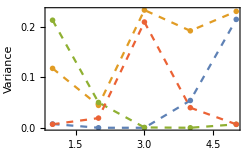

SubtaskVariance.eps

```mathematica
ListLinePlot[{ba,bc,aa,ac},PlotMarkers->{●},PlotStyle->Dashed,PlotRange->All,Frame->True,ImageSize->250,FrameLabel->{"Neuron","Variance"}]
Export["SubtaskVariance.eps",%]
```

```mathematica
{EuclideanDistance[ba,bc],EuclideanDistance[aa,ac],EuclideanDistance[ba,aa],EuclideanDistance[bc,ac],EuclideanDistance[ba,ac],EuclideanDistance[ba,aa]}
```

{0.295563,0.297003,0.300797,0.293771,0.295352,0.300797}

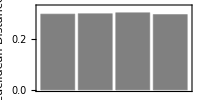

SubtaskEucMI.eps

```mathematica
BarChart[{EuclideanDistance[ba,bc],EuclideanDistance[aa,ac],EuclideanDistance[ba,aa],EuclideanDistance[bc,ac]},ChartStyle->{Gray},FrameLabel->{"","Euclidean Distance"},AspectRatio->1/2,PlotRange->{{0.5,4.5},{0.0,0.325}},Frame->True,ImageSize->200]
Export["SubtaskEucMI.eps",%]
```

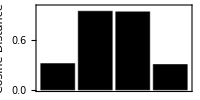

SubtaskCosMI.eps

```mathematica
BarChart[{CosineDistance[ba,bc],CosineDistance[aa,ac],CosineDistance[ba,aa],CosineDistance[bc,ac]},FrameLabel->{"","Cosine Distance"},AspectRatio->1/2,ChartStyle->{Black},PlotRange->{{0.5,4.5},{0.0,1.0}},Frame->True,ImageSize->200]
Export["SubtaskCosMI.eps",%]
```

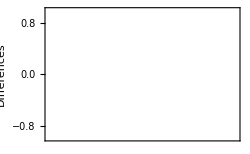

variance_diff.eps

```mathematica
DistributionChart[{baV-bcV,aaV-acV,baV-aaV,bcV-acV},ChartStyle->"SouthwestColors",ChartElementFunction->"HistogramDensity",PlotRange->All,FrameLabel->{"","Differences"},Frame->True,ImageSize->250]
Export["variance_diff.eps",%]
```

## v1 .0

## Task 1: Object Recognition

```mathematica
ba1=Import[StringJoin[dir,"B_avoid_n1.dat"]];
ba2=Import[StringJoin[dir,"B_avoid_n2.dat"]];
ba3=Import[StringJoin[dir,"B_avoid_n3.dat"]];
ba4=Import[StringJoin[dir,"B_avoid_n4.dat"]];
ba5=Import[StringJoin[dir,"B_avoid_n5.dat"]];
bc1=Import[StringJoin[dir,"B_catch_n1.dat"]];
bc2=Import[StringJoin[dir,"B_catch_n2.dat"]];
bc3=Import[StringJoin[dir,"B_catch_n3.dat"]];
bc4=Import[StringJoin[dir,"B_catch_n4.dat"]];
bc5=Import[StringJoin[dir,"B_catch_n5.dat"]];
```

### Neural Variance in General

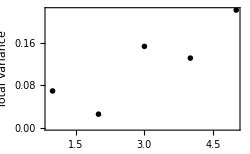

```mathematica
ListPlot[
{Variance[Flatten[Catenate[{ba1,bc1}]]],Variance[Flatten[Catenate[{ba2,bc2}]]],Variance[Flatten[Catenate[{ba3,bc3}]]],Variance[Flatten[Catenate[{ba4,bc4}]]],Variance[Flatten[Catenate[{ba5,bc5}]]]}
,PlotRange->All,Frame->True,FrameLabel->{"Neuron","Total Variance"},ImageSize->250,PlotStyle->Black,PlotMarkers->{●}]
Export["B_Var_General.eps",%];
```

### Neural Variance Across the Task

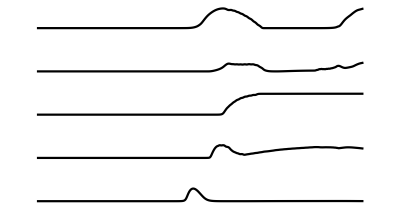

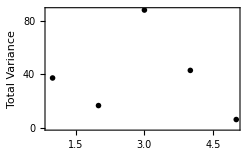

```mathematica
max=0.3;
GraphicsColumn[
{
Show[{
ListLinePlot[Variance[Catenate[{ba1,bc1}]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[Catenate[{ba2,bc2}]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[Catenate[{ba3,bc3}]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[Catenate[{ba4,bc4}]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[Catenate[{ba5,bc5}]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
}
]
Export["B_Var_Task_Traces.eps",%];
ListPlot[
{Total[Variance[Catenate[{ba1,bc1}]]],Total[Variance[Catenate[{ba2,bc2}]]],Total[Variance[Catenate[{ba3,bc3}]]],Total[Variance[Catenate[{ba4,bc4}]]],Total[Variance[Catenate[{ba5,bc5}]]]}
,PlotRange->All,Frame->True,FrameLabel->{"Neuron","Total Variance"},ImageSize->250,PlotStyle->Black,PlotMarkers->{●}]
Export["B_Var_Task_Values.eps",%];
```

### Neural Variance per Subtask

```mathematica
max = 0.25;
```

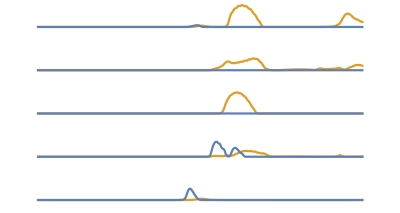

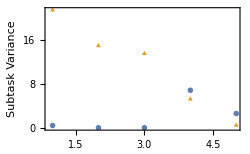

```mathematica
GraphicsColumn[
{
Show[{
ListLinePlot[Variance[bc1],PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[Variance[ba1],PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[bc2],PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[Variance[ba2],PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[bc3],PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[Variance[ba3],PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[bc4],PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[Variance[ba4],PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[bc5],PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[Variance[ba5],PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
}
]
Export["B_Var_SubTask_Traces.eps",%];
ListPlot[{{Total[Variance[ba1]],Total[Variance[ba2]],Total[Variance[ba3]],Total[Variance[ba4]],Total[Variance[ba5]]},
{Total[Variance[bc1]],Total[Variance[bc2]],Total[Variance[bc3]],Total[Variance[bc4]],Total[Variance[bc5]]}},PlotRange->All,Frame->True,FrameLabel->{"Neuron","Subtask Variance"},ImageSize->250,PlotMarkers->{●,▲}]
Export["B_Var_SubTask_Values.eps",%];
```

## Task 2: Perceiving Affordances

```mathematica
aa1=Import[StringJoin[dir,"A_avoid_n1.dat"]];
aa2=Import[StringJoin[dir,"A_avoid_n2.dat"]];
aa3=Import[StringJoin[dir,"A_avoid_n3.dat"]];
aa4=Import[StringJoin[dir,"A_avoid_n4.dat"]];
aa5=Import[StringJoin[dir,"A_avoid_n5.dat"]];
ac1=Import[StringJoin[dir,"A_pass_n1.dat"]];
ac2=Import[StringJoin[dir,"A_pass_n2.dat"]];
ac3=Import[StringJoin[dir,"A_pass_n3.dat"]];
ac4=Import[StringJoin[dir,"A_pass_n4.dat"]];
ac5=Import[StringJoin[dir,"A_pass_n5.dat"]];
```

### Neural Variance in General

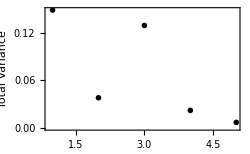

```mathematica
ListPlot[
{Variance[Flatten[Catenate[{aa1,ac1}]]],Variance[Flatten[Catenate[{aa2,ac2}]]],Variance[Flatten[Catenate[{aa3,ac3}]]],Variance[Flatten[Catenate[{aa4,ac4}]]],Variance[Flatten[Catenate[{aa5,ac5}]]]}
,PlotRange->All,Frame->True,FrameLabel->{"Neuron","Total Variance"},ImageSize->250,PlotStyle->Black,PlotMarkers->"OpenMarkers"]
Export["A_Var_General.eps",%];
```

### Neural Variance Across the Task

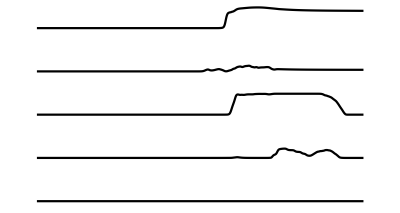

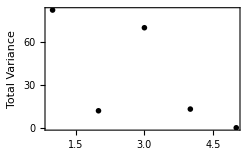

```mathematica
max=0.3;
GraphicsColumn[
{
Show[{
ListLinePlot[Variance[Catenate[{aa1,ac1}]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[Catenate[{aa2,ac2}]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[Catenate[{aa3,ac3}]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[Catenate[{aa4,ac4}]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[Catenate[{aa5,ac5}]],PlotStyle->Black,PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
}
]
Export["A_Var_Task_Traces.eps",%];
ListPlot[
{Total[Variance[Catenate[{aa1,ac1}]]],Total[Variance[Catenate[{aa2,ac2}]]],Total[Variance[Catenate[{aa3,ac3}]]],Total[Variance[Catenate[{aa4,ac4}]]],Total[Variance[Catenate[{aa5,ac5}]]]}
,PlotRange->All,Frame->True,FrameLabel->{"Neuron","Total Variance"},ImageSize->250,PlotStyle->Black,PlotMarkers->"OpenMarkers"]
Export["A_Var_Task_Values.eps",%];
```

### Neural Variance per Subtask

```mathematica
max = 0.25;
```

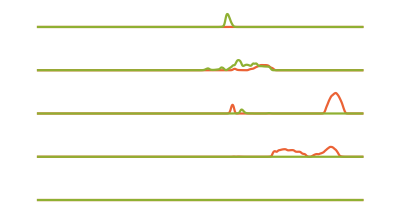

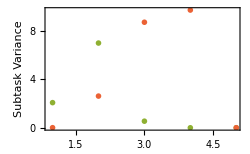

```mathematica
GraphicsColumn[
{
Show[{
ListLinePlot[Variance[ac1],PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[Variance[aa1],PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[ac2],PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[Variance[aa2],PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[ac3],PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[Variance[aa3],PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[ac4],PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[Variance[aa4],PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[ac5],PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[Variance[aa5],PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
}
]
Export["A_Var_SubTask_Traces.eps",%];
ListPlot[{{Total[Variance[aa1]],Total[Variance[aa2]],Total[Variance[aa3]],Total[Variance[aa4]],Total[Variance[aa5]]},
{Total[Variance[ac1]],Total[Variance[ac2]],Total[Variance[ac3]],Total[Variance[ac4]],Total[Variance[ac5]]}},PlotStyle->{cd[[3]],cd[[4]]},PlotRange->All,Frame->True,FrameLabel->{"Neuron","Subtask Variance"},ImageSize->250,PlotMarkers->"OpenMarkers"]
Export["A_Var_SubTask_Values.eps",%];
```

## Together

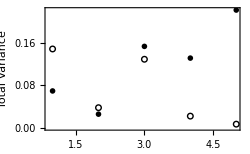

```mathematica
ListPlot[{
{Variance[Flatten[Catenate[{ba1,bc1}]]],Variance[Flatten[Catenate[{ba2,bc2}]]],Variance[Flatten[Catenate[{ba3,bc3}]]],Variance[Flatten[Catenate[{ba4,bc4}]]],Variance[Flatten[Catenate[{ba5,bc5}]]]},
{Variance[Flatten[Catenate[{aa1,ac1}]]],Variance[Flatten[Catenate[{aa2,ac2}]]],Variance[Flatten[Catenate[{aa3,ac3}]]],Variance[Flatten[Catenate[{aa4,ac4}]]],Variance[Flatten[Catenate[{aa5,ac5}]]]}
},PlotRange->All,Frame->True,FrameLabel->{"Neuron","Total Variance"},ImageSize->250,PlotStyle->Black,PlotMarkers->{●,○}]
Export["TotalCombinedVar.eps",%];
```

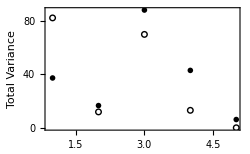

```mathematica
ListPlot[
{{Total[Variance[Catenate[{ba1,bc1}]]],Total[Variance[Catenate[{ba2,bc2}]]],Total[Variance[Catenate[{ba3,bc3}]]],Total[Variance[Catenate[{ba4,bc4}]]],Total[Variance[Catenate[{ba5,bc5}]]]},
{Total[Variance[Catenate[{aa1,ac1}]]],Total[Variance[Catenate[{aa2,ac2}]]],Total[Variance[Catenate[{aa3,ac3}]]],Total[Variance[Catenate[{aa4,ac4}]]],Total[Variance[Catenate[{aa5,ac5}]]]}
}
,PlotRange->All,Frame->True,FrameLabel->{"Neuron","Total Variance"},ImageSize->250,PlotStyle->Black,PlotMarkers->{●,○}]
Export["TotalTaskVar.eps",%];
```

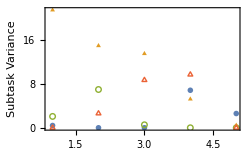

```mathematica
ListPlot[{{Total[Variance[ba1]],Total[Variance[ba2]],Total[Variance[ba3]],Total[Variance[ba4]],Total[Variance[ba5]]},
{Total[Variance[bc1]],Total[Variance[bc2]],Total[Variance[bc3]],Total[Variance[bc4]],Total[Variance[bc5]]},
{Total[Variance[aa1]],Total[Variance[aa2]],Total[Variance[aa3]],Total[Variance[aa4]],Total[Variance[aa5]]},
{Total[Variance[ac1]],Total[Variance[ac2]],Total[Variance[ac3]],Total[Variance[ac4]],Total[Variance[ac5]]}
},PlotRange->All,Frame->True,FrameLabel->{"Neuron","Subtask Variance"},ImageSize->250,PlotMarkers->{●,▲,○,△}]
Export["SubTask_Values.eps",%];
```